```mathematica
rawData=Import["C:\\Users\\Jason\\Documents\\Waveforms\\20210809-0002.csv"];
```

```mathematica
Take[rawData,2]
```

{{Time,Channel A,Channel B,D0},{(ms),(V),(mV),(Binary)}}

```mathematica
rawData⟦4⟧
```

{-10.,0.519685,0.,0}

```mathematica
rawData⟦-1⟧
```

{10.,0.519685,-0.15748,0}

```mathematica
data={#1,#2}&@@@Drop[rawData,3];
```

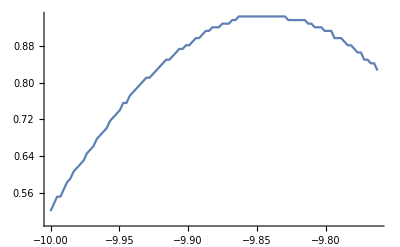

```mathematica
ListLinePlot[data⟦1;;10000;;100⟧]
```

```mathematica
{Mean[#],StandardDeviation[#]}&@(data⟦2;;1001,1⟧-data⟦1;;1000,1⟧)
```

{0.000024,5.60484×10^-16}

```mathematica
0.00002400000000000091milli seconds//in[nano]
```

24. nano seconds

```mathematica
(0.00002400000000000091milli seconds)^-1//in[Mega Hz]
```

41.6667 Hz Mega